# List #4

## Exercise 1

We draw an ellipse:

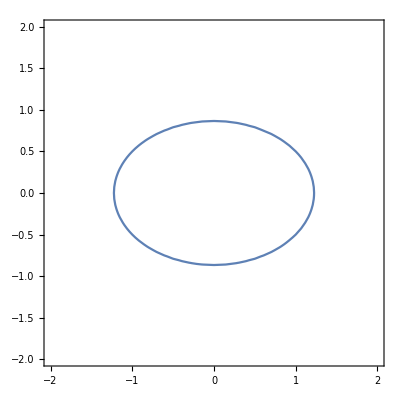

```mathematica
b=3/4;
a=2b;
ContourPlot[x^2/a+y^2/b==1,{x,-2,2},{y,-2,2}]
```

## Exercise 2

We draw Monkey Saddle:

```mathematica
f[x_,y_]:=x y^2-x^3
Animate[Plot3D[f[x,y],{x,-10,10},{y,-10,10},Boxed->True,ViewPoint->{-7Cos[2 Pi k/10], -7 Sin[2 Pi k/10], 3},BoxRatios->{1,1 , 1},Axes->{True,True,False}],{k,1,10},AnimationRate->0.3]
```

## Exercise 3

We draw a little bit modified Monkey Saddle:

```mathematica
g[x_,y_,t_]:=(x+t)(x^2-3 y^2)
saddlelist=Table[Plot3D[g[x,y,t],{x,-10,10},{y,-10,10}],{t,-12,12,1}];
ListAnimate[saddlelist,40,AnimationRate->0.3]
```

## Exercise 4

We compute Van der Pol equation:

```mathematica
vdp=
```